### Start choosing the example:

```mathematica
t=27;
beta = 1;
A = 0.2;
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

x

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Data["Entrance Vertices and Currents"]={{1,65}};
Data["Exit Vertices and Terminal Costs"]={{10,0}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.014444,Null}

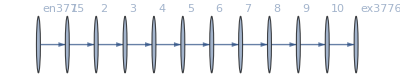

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j3777→65.,j3778→65.,j3779→65.,j3780→65.,j3781→65.,j3782→65.,j3783→65.,j3784→65.,j3785→65.,j3786→65.,j3787→65.,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65.,jt3801→65.,jt3802→0.,jt3803→65.,jt3804→0.,jt3805→65.,jt3806→0.,jt3807→65.,jt3808→0.,jt3809→65.,jt3810→0.,jt3811→65.,jt3812→0.,jt3813→65.,jt3814→0.,jt3815→65.,jt3816→0.,jt3817→65.,jt3818→0.,u3819→585.,u3820→520.,u3821→455.,u3822→390.,u3823→325.,u3824→260.,u3825→195.,u3826→130.,u3827→65.,u3828→0.,u3829→585.,u3830→520.,u3831→455.,u3832→390.,u3833→325.,u3834→260.,u3835→195.,u3836→130.,u3837→65.,u3838→0.,u3839→0.,u3840→585.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→45.4737,u3820→40.4211,u3821→35.3685,u3822→30.3158,u3823→25.2632,u3824→20.2105,u3825→15.1579,u3826→10.1053,u3827→5.05264,u3828→0.,u3829→45.4737,u3830→40.4211,u3831→35.3685,u3832→30.3158,u3833→25.2632,u3834→20.2105,u3835→15.1579,u3836→10.1053,u3837→5.05264,u3838→0,u3839→0.,u3840→45.4737|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.03649×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.03649×10^-17

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→54.245,u3820→48.2177,u3821→42.1905,u3822→36.1633,u3823→30.1361,u3824→24.1089,u3825→18.0817,u3826→12.0544,u3827→6.02722,u3828→0.,u3829→54.245,u3830→48.2177,u3831→42.1905,u3832→36.1633,u3833→30.1361,u3834→24.1089,u3835→18.0817,u3836→12.0544,u3837→6.02722,u3838→0,u3839→0.,u3840→54.245|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.2172×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.2172×10^-16

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→80.262,u3820→71.344,u3821→62.426,u3822→53.508,u3823→44.59,u3824→35.672,u3825→26.754,u3826→17.836,u3827→8.918,u3828→0.,u3829→80.262,u3830→71.344,u3831→62.426,u3832→53.508,u3833→44.59,u3834→35.672,u3835→26.754,u3836→17.836,u3837→8.918,u3838→0,u3839→0.,u3840→80.262|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→406.236,u3820→361.099,u3821→315.961,u3822→270.824,u3823→225.687,u3824→180.549,u3825→135.412,u3826→90.2746,u3827→45.1373,u3828→0.,u3829→406.236,u3830→361.099,u3831→315.961,u3832→270.824,u3833→225.687,u3834→180.549,u3835→135.412,u3836→90.2746,u3837→45.1373,u3838→0,u3839→0.,u3840→406.236|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.13163×10^-13

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→585.,u3820→520.,u3821→455.,u3822→390.,u3823→325.,u3824→260.,u3825→195.,u3826→130.,u3827→65.,u3828→0.,u3829→585.,u3830→520.,u3831→455.,u3832→390.,u3833→325.,u3834→260.,u3835→195.,u3836→130.,u3837→65.,u3838→0,u3839→0.,u3840→585.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.62976×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.62976×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→1369.77,u3820→1217.57,u3821→1065.37,u3822→913.177,u3823→760.981,u3824→608.785,u3825→456.589,u3826→304.392,u3827→152.196,u3828→0.,u3829→1369.77,u3830→1217.57,u3831→1065.37,u3832→913.177,u3833→760.981,u3834→608.785,u3835→456.589,u3836→304.392,u3837→152.196,u3838→0,u3839→0.,u3840→1369.77|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.57114×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.57114×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→7507.74,u3820→6673.55,u3821→5839.36,u3822→5005.16,u3823→4170.97,u3824→3336.77,u3825→2502.58,u3826→1668.39,u3827→834.194,u3828→0.,u3829→7507.74,u3830→6673.55,u3831→5839.36,u3832→5005.16,u3833→4170.97,u3834→3336.77,u3835→2502.58,u3836→1668.39,u3837→834.194,u3838→0,u3839→0.,u3840→7507.74|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.45215×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.45215×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→15564.9,u3820→13835.5,u3821→12106.1,u3822→10376.6,u3823→8647.18,u3824→6917.75,u3825→5188.31,u3826→3458.87,u3827→1729.44,u3828→0.,u3829→15564.9,u3830→13835.5,u3831→12106.1,u3832→10376.6,u3833→8647.18,u3834→6917.75,u3835→5188.31,u3836→3458.87,u3837→1729.44,u3838→0,u3839→0.,u3840→15564.9|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.85655×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.85655×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→15577.1,u3820→13846.3,u3821→12115.5,u3822→10384.7,u3823→8653.94,u3824→6923.15,u3825→5192.37,u3826→3461.58,u3827→1730.79,u3828→0.,u3829→15577.1,u3830→13846.3,u3831→12115.5,u3832→10384.7,u3833→8653.94,u3834→6923.15,u3835→5192.37,u3836→3461.58,u3837→1730.79,u3838→0,u3839→0.,u3840→15577.1|>

```mathematica
alpha = 1.605;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.39424×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.39424×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→16187.2,u3820→14388.6,u3821→12590.,u3822→10791.4,u3823→8992.87,u3824→7194.29,u3825→5395.72,u3826→3597.15,u3827→1798.57,u3828→0.,u3829→16187.2,u3830→14388.6,u3831→12590.,u3832→10791.4,u3833→8992.87,u3834→7194.29,u3835→5395.72,u3836→3597.15,u3837→1798.57,u3838→0,u3839→0.,u3840→16187.2|>

```mathematica
alpha = 1.61;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.03819×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.03819×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→16839.,u3820→14968.,u3821→13097.,u3822→11226.,u3823→9355.01,u3824→7484.01,u3825→5613.,u3826→3742.,u3827→1871.,u3828→0.,u3829→16839.,u3830→14968.,u3831→13097.,u3832→11226.,u3833→9355.01,u3834→7484.01,u3835→5613.,u3836→3742.,u3837→1871.,u3838→0,u3839→0.,u3840→16839.|>

```mathematica
alpha = 1.62;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.55905×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.55905×10^-16

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→18238.2,u3820→16211.7,u3821→14185.2,u3822→12158.8,u3823→10132.3,u3824→8105.85,u3825→6079.39,u3826→4052.93,u3827→2026.46,u3828→0.,u3829→18238.2,u3830→16211.7,u3831→14185.2,u3832→12158.8,u3833→10132.3,u3834→8105.85,u3835→6079.39,u3836→4052.93,u3837→2026.46,u3838→0,u3839→0.,u3840→18238.2|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→23337.6,u3820→20744.5,u3821→18151.5,u3822→15558.4,u3823→12965.3,u3824→10372.3,u3825→7779.2,u3826→5186.13,u3827→2593.07,u3828→0.,u3829→23337.6,u3830→20744.5,u3831→18151.5,u3832→15558.4,u3833→12965.3,u3834→10372.3,u3835→7779.2,u3836→5186.13,u3837→2593.07,u3838→0,u3839→0.,u3840→23337.6|>

```mathematica
alpha = 1.7;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.22504×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.22504×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→36099.1,u3820→32088.,u3821→28077.,u3822→24066.,u3823→20055.,u3824→16044.,u3825→12033.,u3826→8022.01,u3827→4011.01,u3828→0.,u3829→36099.1,u3830→32088.,u3831→28077.,u3832→24066.,u3833→20055.,u3834→16044.,u3835→12033.,u3836→8022.01,u3837→4011.01,u3838→0,u3839→0.,u3840→36099.1|>

```mathematica
alpha = 1.8;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.41006×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.41006×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→96324.4,u3820→85621.6,u3821→74918.9,u3822→64216.2,u3823→53513.5,u3824→42810.8,u3825→32108.1,u3826→21405.4,u3827→10702.7,u3828→0.,u3829→96324.4,u3830→85621.6,u3831→74918.9,u3832→64216.2,u3833→53513.5,u3834→42810.8,u3835→32108.1,u3836→21405.4,u3837→10702.7,u3838→0,u3839→0.,u3840→96324.4|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.47946×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.47946×10^-15

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→307240.,u3820→273102.,u3821→238964.,u3822→204827.,u3823→170689.,u3824→136551.,u3825→102413.,u3826→68275.6,u3827→34137.8,u3828→0.,u3829→307240.,u3830→273102.,u3831→238964.,u3832→204827.,u3833→170689.,u3834→136551.,u3835→102413.,u3836→68275.6,u3837→34137.8,u3838→0,u3839→0.,u3840→307240.|>

```mathematica
alpha = 1.91;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5(*,SameTest-> (Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.04964×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.04964×10^-16

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→349089.,u3820→310301.,u3821→271513.,u3822→232726.,u3823→193938.,u3824→155151.,u3825→116363.,u3826→77575.3,u3827→38787.6,u3828→0.,u3829→349089.,u3830→310301.,u3831→271513.,u3832→232726.,u3833→193938.,u3834→155151.,u3835→116363.,u3836→77575.3,u3837→38787.6,u3838→0,u3839→0.,u3840→349089.|>

```mathematica
alpha = 1.99;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5(*,SameTest-> (Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.21443×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.21443×10^-16

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→1.06203×10^6,u3820→944027.,u3821→826023.,u3822→708020.,u3823→590017.,u3824→472013.,u3825→354010.,u3826→236007.,u3827→118003.,u3828→0.,u3829→1.06203×10^6,u3830→944027.,u3831→826023.,u3832→708020.,u3833→590017.,u3834→472013.,u3835→354010.,u3836→236007.,u3837→118003.,u3838→0,u3839→0.,u3840→1.06203×10^6|>

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/IterationFunction.m"];
```

```mathematica
alpha =2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],500(*,SameTest-> (Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.53406×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.53406×10^-16

<|j3777→65,j3778→65,j3779→65,j3780→65,j3781→65,j3782→65,j3783→65,j3784→65,j3785→65,j3786→65,j3787→65,j3788→0.,j3789→0.,j3790→0.,j3791→0.,j3792→0.,j3793→0.,j3794→0.,j3795→0.,j3796→0.,j3797→0.,j3798→0.,jt3799→0.,jt3800→65,jt3801→65,jt3802→0.,jt3803→65,jt3804→0.,jt3805→65,jt3806→0.,jt3807→65,jt3808→0.,jt3809→65,jt3810→0.,jt3811→65,jt3812→0.,jt3813→65,jt3814→0.,jt3815→65,jt3816→0.,jt3817→65,jt3818→0.,u3819→1.23587×10^6,u3820→1.09855×10^6,u3821→961233.,u3822→823914.,u3823→686595.,u3824→549276.,u3825→411957.,u3826→274638.,u3827→137319.,u3828→0.,u3829→1.23587×10^6,u3830→1.09855×10^6,u3831→961233.,u3832→823914.,u3833→686595.,u3834→549276.,u3835→411957.,u3836→274638.,u3837→137319.,u3838→0,u3839→0.,u3840→1.23587×10^6|>

```mathematica
aux = <|j2603->65,u2655->0.,j2593->65,j2594->65,j2595->65,j2596->65,j2597->65,j2598->65,j2599->65,j2600->65,j2601->65,j2602->65,j2604->0.,j2605->0.,j2606->0.,j2607->0.,j2608->0.,j2609->0.,j2610->0.,j2611->0.,j2612->0.,j2613->0.,j2614->0.,jt2615->0.,jt2616->65,jt2617->65,jt2618->0.,jt2619->65,jt2620->0.,jt2621->65,jt2622->0.,jt2623->65,jt2624->0.,jt2625->65,jt2626->0.,jt2627->65,jt2628->0.,jt2629->65,jt2630->0.,jt2631->65,jt2632->0.,jt2633->65,jt2634->0.,u2644->0.,u2656->0.+1. (0.+1. 7.153383732831773*^19),u2645->0.+1. 7.153383732831773*^19,u2646->6.358563318072687*^19,u2647->5.5637429033136005*^19,u2648->4.768922488554515*^19,u2649->3.974102073795428*^19,u2650->3.1792816590363427*^19,u2651->2.384461244277257*^19,u2652->1.5896408295181713*^19,u2653->7.948204147590857*^18,u2654->0,u2635->7.153383732831773*^19,u2636->6.358563318072687*^19,u2637->5.5637429033136005*^19,u2638->4.768922488554515*^19,u2639->3.974102073795428*^19,u2640->3.1792816590363427*^19,u2641->2.384461244277257*^19,u2642->1.5896408295181713*^19,u2643->7.948204147590857*^18|>;
```

```mathematica
MFGEquations["Nlhs"]/MFGEquations["Nrhs"]
MFGEquations["Nlhs"]/.aux

MFGEquations["Nrhs"]/.aux
(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nrhs"]/.aux
```

{(j3777-j3788-u3819+u3830)/(j3777-j3788+IntM[j3777-j3788]),(j3778-j3789-u3820+u3831)/(j3778-j3789+IntM[j3778-j3789]),(j3779-j3790-u3821+u3832)/(j3779-j3790+IntM[j3779-j3790]),(j3780-j3791-u3822+u3833)/(j3780-j3791+IntM[j3780-j3791]),(j3781-j3792-u3823+u3834)/(j3781-j3792+IntM[j3781-j3792]),(j3782-j3793-u3824+u3835)/(j3782-j3793+IntM[j3782-j3793]),(j3783-j3794-u3825+u3836)/(j3783-j3794+IntM[j3783-j3794]),(j3784-j3795-u3826+u3837)/(j3784-j3795+IntM[j3784-j3795]),(j3785-j3796-u3827+u3838)/(j3785-j3796+IntM[j3785-j3796])}

{j3777-j3788-u3819+u3830,j3778-j3789-u3820+u3831,j3779-j3790-u3821+u3832,j3780-j3791-u3822+u3833,j3781-j3792-u3823+u3834,j3782-j3793-u3824+u3835,j3783-j3794-u3825+u3836,j3784-j3795-u3826+u3837,j3785-j3796-u3827+u3838}

{j3777-j3788+IntM[j3777-j3788],j3778-j3789+IntM[j3778-j3789],j3779-j3790+IntM[j3779-j3790],j3780-j3791+IntM[j3780-j3791],j3781-j3792+IntM[j3781-j3792],j3782-j3793+IntM[j3782-j3793],j3783-j3794+IntM[j3783-j3794],j3784-j3795+IntM[j3784-j3795],j3785-j3796+IntM[j3785-j3796]}

{(-u3819+u3830-IntM[j3777-j3788])/(j3777-j3788+IntM[j3777-j3788]),(-u3820+u3831-IntM[j3778-j3789])/(j3778-j3789+IntM[j3778-j3789]),(-u3821+u3832-IntM[j3779-j3790])/(j3779-j3790+IntM[j3779-j3790]),(-u3822+u3833-IntM[j3780-j3791])/(j3780-j3791+IntM[j3780-j3791]),(-u3823+u3834-IntM[j3781-j3792])/(j3781-j3792+IntM[j3781-j3792]),(-u3824+u3835-IntM[j3782-j3793])/(j3782-j3793+IntM[j3782-j3793]),(-u3825+u3836-IntM[j3783-j3794])/(j3783-j3794+IntM[j3783-j3794]),(-u3826+u3837-IntM[j3784-j3795])/(j3784-j3795+IntM[j3784-j3795]),(-u3827+u3838-IntM[j3785-j3796])/(j3785-j3796+IntM[j3785-j3796])}

### What we this plot for?

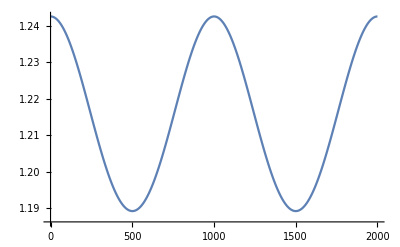

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.